Part 6: Simulation Result Analysis

```mathematica
(*Produces just an array with either probability (flag=0) or helmholtz free energy (flag=1)*)

simProbs = Import["/Users/rachelkrueger/Documents/StatMech/probs_traj1.dat"]
```

{{0,0.277741},{1,0.214981},{2,0.125051},{3,0.063958},{4,0.030514},{5,0.287755}}

```mathematica
(*comparing to a million-step trajectory*)
```

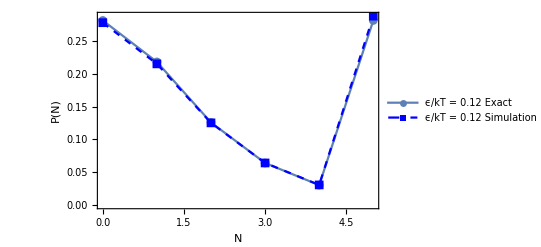

```mathematica
simCompare12 =ListLinePlot[{getDist[1.2,0.12,1],simProbs},PlotMarkers->Automatic,FrameLabel->{"N","P(N)"},PlotLegends->{"ϵ/kT = 0.12 Exact","ϵ/kT = 0.12 Simulation"},BaseStyle->{FontSize->14},PlotStyle->{{Darker Blue},{Blue,Dashed}},Frame->True]
```

```mathematica
simProbs08 = Import["/Users/rachelkrueger/Documents/StatMech/probs_08single.dat"]
```

{{0,0.11147},{1,0.12273},{2,0.09707},{3,0.065},{4,0.04439},{5,0.55934}}

```mathematica
simProbs15 = Import["/Users/rachelkrueger/Documents/StatMech/probs_15single.dat"]
```

{{0,0.41942},{1,0.25848},{2,0.1131},{3,0.0471},{4,0.01872},{5,0.14318}}

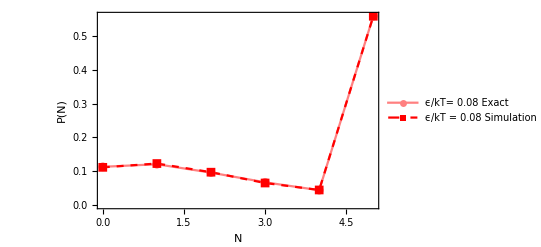

```mathematica
simCompare08 =ListLinePlot[{getDist[1.2,0.08,1],simProbs08},BaseStyle->{FontSize->14},PlotMarkers->Automatic,FrameLabel->{"N","P(N)"},PlotLegends->{"ϵ/kT= 0.08 Exact","ϵ/kT = 0.08 Simulation"},PlotStyle->{{Pink},{Red,Dashed}},Frame->True,PlotRange->All]
```

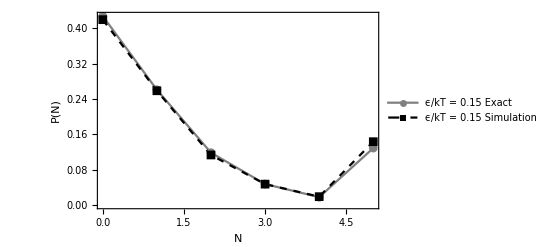

```mathematica
simCompare15 =ListLinePlot[{getDist[1.2,0.15,1],simProbs15},PlotMarkers->Automatic,FrameLabel->{"N","P(N)"},BaseStyle->{FontSize->14},PlotLegends->{"ϵ/kT = 0.15 Exact","ϵ/kT = 0.15 Simulation"},PlotStyle->{{Gray},{Black,Dashed}},Frame->True]
```

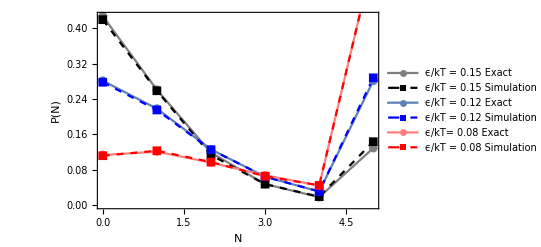

```mathematica
compareAll=Show[{simCompare15,simCompare12, simCompare08}]
```

```mathematica
Export["/Users/rachelkrueger/Documents/StatMech/fig9.eps",compareAll]
```

/Users/rachelkrueger/Documents/StatMech/fig9.eps

```mathematica
traj=Import["/Users/rachelkrueger/Documents/StatMech/traj11600.dat"]
```

{{0,0,2,-1,-1,-1,-1,-1},{1,0,2,-1,-1,-1,-1,-1},{2,0,2,-1,-1,-1,-1,-1},{3,1,2,1,-1,-1,-1,-1},{4,1,2,1,-1,-1,-1,-1},{5,2,2,1,-1,-1,-1,1},{6,3,2,1,1,-1,-1,1},{7,2,2,1,-1,-1,-1,1},{8,2,2,1,-1,-1,-1,1},1581,{1590,3,2,1,-1,-1,1,1},{1591,2,2,-1,-1,-1,1,1},{1592,3,2,-1,-1,1,1,1},{1593,3,2,-1,-1,1,1,1},{1594,4,2,-1,1,1,1,1},{1595,4,2,-1,1,1,1,1},{1596,4,2,-1,1,1,1,1},{1597,4,2,-1,1,1,1,1},{1598,4,2,-1,1,1,1,1}}
 |  |  |  |

```mathematica
(*averaged over 1000 simulations*)
```

```mathematica
avg12=Import["/Users/rachelkrueger/Documents/StatMech/av12.dat"]
```

{{0,0,2},{1,0.15,2.006},{2,0.272,2.008},{3,0.37,2.008},{4,0.451,2.014},{5,0.55,2.016},{6,0.619,2.012},{7,0.651,2},{8,0.697,1.998},{9,0.756,1.998},9981,{9991,2.152,1.488},{9992,2.137,1.48},{9993,2.131,1.486},{9994,2.137,1.488},{9995,2.115,1.498},{9996,2.122,1.486},{9997,2.116,1.48},{9998,2.109,1.48},{9999,2.089,1.482}}
 |  |  |  |

```mathematica
avg08=Import["/Users/rachelkrueger/Documents/StatMech/av08.dat"]
```

{{0,0,2},{1,0.204,2.004},{2,0.376,2.002},{3,0.525,2.006},{4,0.663,2.012},{5,0.777,2.014},{6,0.875,2.008},{7,0.944,2},{8,0.995,2},{9,1.064,1.992},9981,{9991,3.462,0.896},{9992,3.455,0.898},{9993,3.462,0.896},{9994,3.479,0.884},{9995,3.458,0.892},{9996,3.452,0.892},{9997,3.459,0.904},{9998,3.468,0.9},{9999,3.479,0.888}}
 |  |  |  |

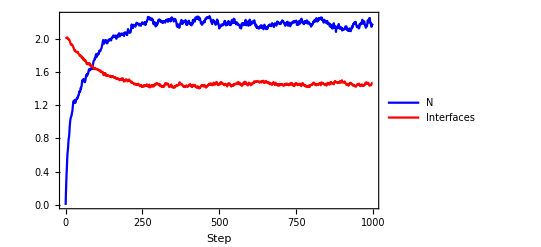

```mathematica
niOfT12=ListLinePlot[{avg12[[1;;1000,{1,2}]],avg12[[1;;1000,{1,3}]]},PlotStyle->{Blue,Red},Frame->True,FrameLabel->{"Step",""},PlotLegends->{"N","Interfaces"}]
```

```mathematica
avg15=Import["/Users/rachelkrueger/Documents/StatMech/av15.dat"]
```

{{0,0,2},{1,0.116,2.004},{2,0.212,2.004},{3,0.296,2.006},{4,0.357,2.006},{5,0.408,2.006},{6,0.457,2.012},{7,0.511,2.012},{8,0.535,2.006},9982,{9991,1.335,1.774},{9992,1.368,1.764},{9993,1.361,1.756},{9994,1.338,1.75},{9995,1.348,1.754},{9996,1.335,1.752},{9997,1.319,1.752},{9998,1.33,1.752},{9999,1.291,1.76}}
 |  |  |  |

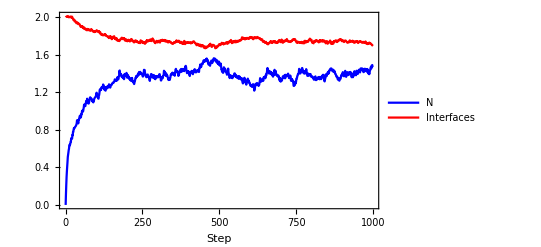

```mathematica
niOfT15=ListLinePlot[{avg15[[1;;1000,{1,2}]],avg15[[1;;1000,{1,3}]]},PlotStyle->{Blue,Red},Frame->True,FrameLabel->{"Step",""},PlotLegends->{"N","Interfaces"}]
```

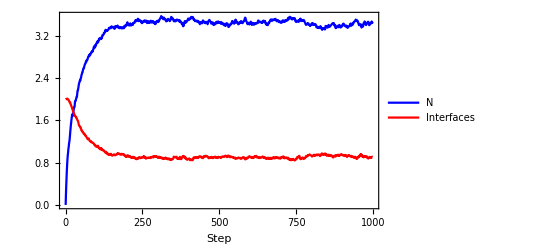

```mathematica
niOfT08=ListLinePlot[{avg08[[1;;1000,{1,2}]],avg08[[1;;1000,{1,3}]]},PlotStyle->{Blue,Red},Frame->True,FrameLabel->{"Step",""},PlotLegends->{"N","Interfaces"}]
```

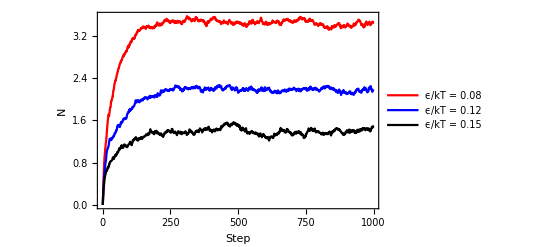

```mathematica
nPlot=ListLinePlot[{avg08[[1;;1000,{1,2}]],avg12[[1;;1000,{1,2}]],avg15[[1;;1000,{1,2}]]},Frame->True,PlotStyle->{Red,Blue,Black},BaseStyle->{FontSize->14},FrameLabel->{"Step","N"},PlotLegends->{"ϵ/kT = 0.08","ϵ/kT = 0.12","ϵ/kT = 0.15"}]
```

```mathematica
Export["/Users/rachelkrueger/Documents/StatMech/fig10.eps",nPlot]
```

/Users/rachelkrueger/Documents/StatMech/fig10.eps

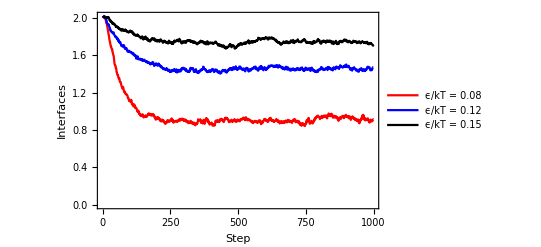

```mathematica
intPlot=ListLinePlot[{avg08[[1;;1000,{1,3}]],avg12[[1;;1000,{1,3}]],avg15[[1;;1000,{1,3}]]},Frame->True,BaseStyle->{FontSize->14},PlotStyle->{Red,Blue,Black},FrameLabel->{"Step","Interfaces"},PlotLegends->{"ϵ/kT = 0.08","ϵ/kT = 0.12","ϵ/kT = 0.15"},PlotRange->All]
```

```mathematica
Export["/Users/rachelkrueger/Documents/StatMech/fig11.eps",intPlot]
```

/Users/rachelkrueger/Documents/StatMech/fig11.eps